```mathematica
StreamPlot[{y - x, x^2}, {x, -10, 10}, {y, -10, 10}]
```

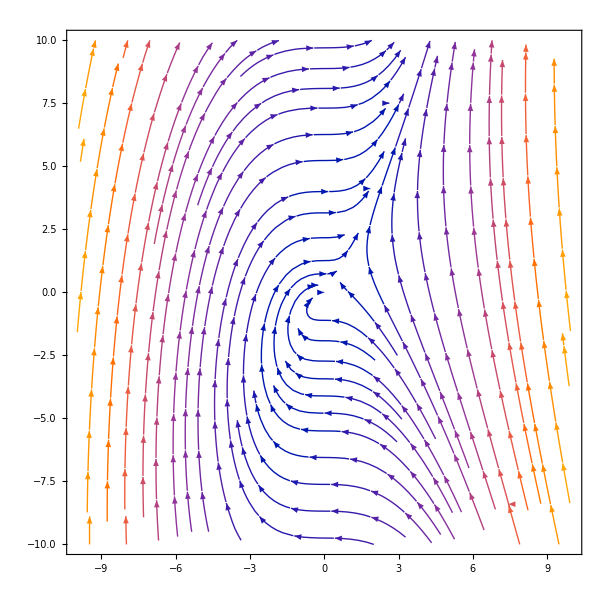

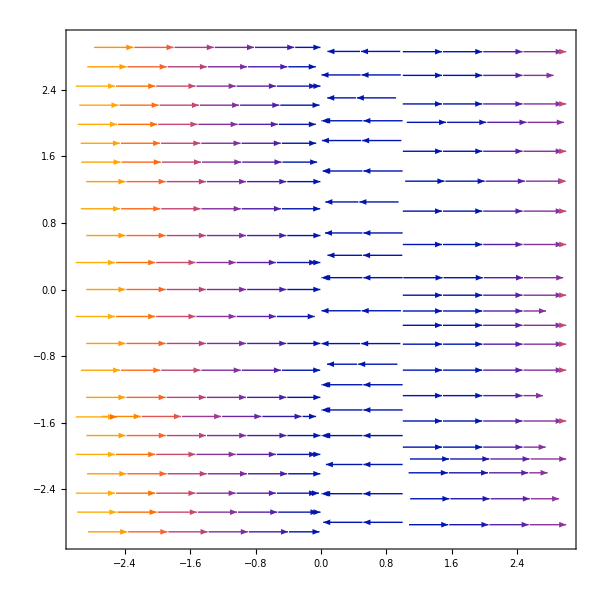

```mathematica
StreamPlot[{a*r + r^2, 0} /. {a -> -1} , {r, -3, 3}, {θ, -3, 3}]
```

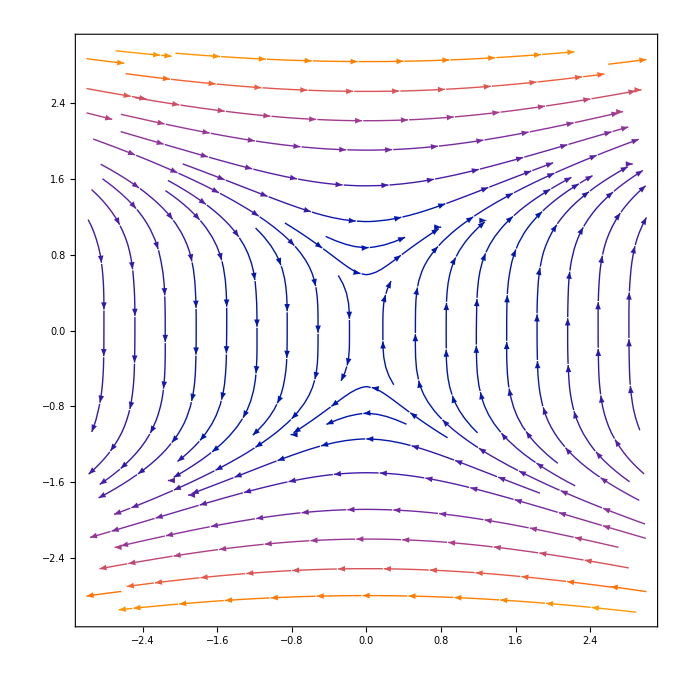

```mathematica
StreamPlot[{y^3, x}, {x, -3, 3}, {y, -3, 3}]
```

2 √((x^2+y^2)^Abs[n])

(2 Tan[n ArcTan[y/x]])/(1+Tan[n ArcTan[y/x]]^2)

0

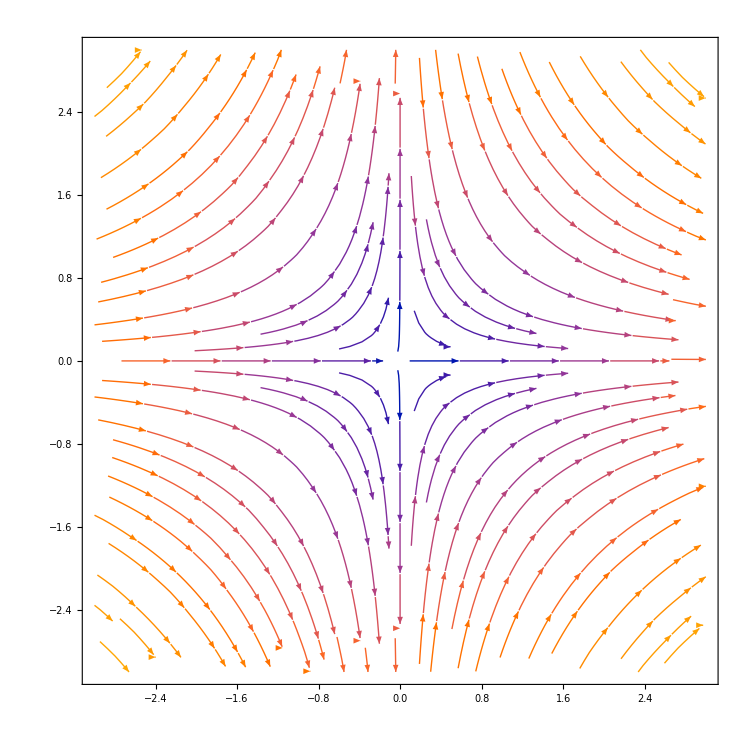

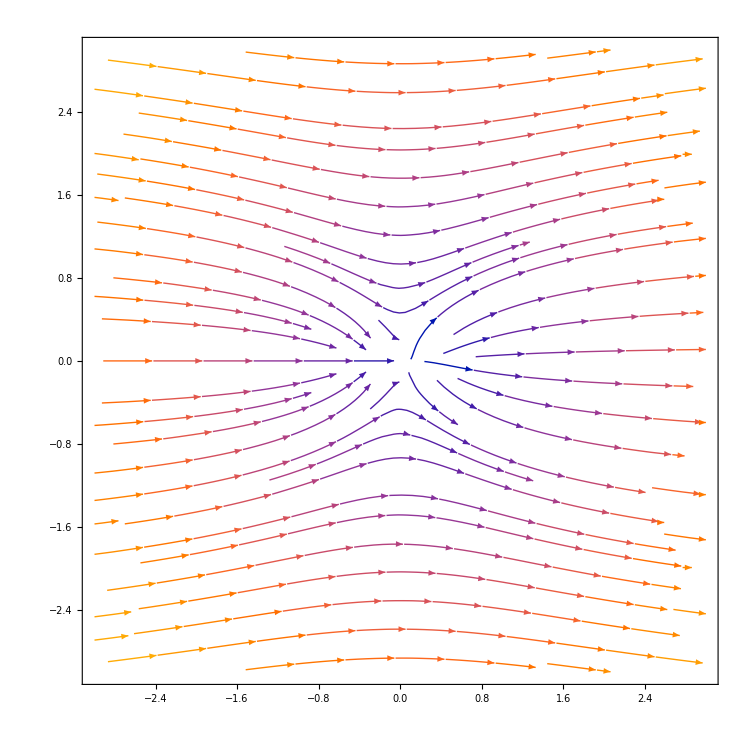

```mathematica
Clear["Global`*"]
n = .;
f[x_, y_] := (x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
g[x_, y_]:=(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
r[x_, y_] := Sqrt[f[x,y]^2 + g[x,y]^2]
drx = Integrate[D[r[x,y], x], x];
dry  = Integrate[D[r[x,y], y], y];
dr[x_, y_] := drx + dry 
dr[x, y]
ϕ[x_,y_] := ArcTan[y/x];
I1 =Integrate[(f[x,y]*D[g[x,y],x]-g[x,y]*D[f[x,y],x])/f[x,y]^2,x];
I2 = Integrate[(f[x,y]*D[g[x,y],y]-g[x,y]*D[f[x,y],y])/f[x,y]^2,y];
dϕ[x_,y_] := 1/(1+(g[x,y]/f[x,y])^2)*(I1+I2)
dϕ[x,y]
index = (Integrate[dϕ[1,y],{y,-1,1}]+Integrate[dϕ[x,1],{x,1,-1}]+Integrate[dϕ[-1,y],{y,1,-1}]+Integrate[dϕ[x,-1],{x,-1,1}])/(2*Pi)
StreamPlot[{f[x,y], g[x,y]}/.n->-1,{x,-3,3},{y,-3,3}]
StreamPlot[{dr[x,y], dϕ[x,y]}/.n->1,{x,-3,3},{y,-3,3}]
```